```mathematica
SetDirectory[FileNameJoin@{ParentDirectory[NotebookDirectory[]],"Shared"}];
Needs["gPlots3DEx`"];
Needs["gPlotsEx`"]; 
Needs["gBRDF`"];
Needs["gUtils`"];
Needs["pbrtShared`"];
Needs["pbrtLog`"];
SetDirectory[NotebookDirectory[]];

gPrint["Origin Scene"];
ClearAll[scene];
scene=pbrtLoadScene["pbrtTestScene.scene"];
Show[pbrtPlotOriginScene[scene],pbrtPlot3DOptions[scene]]
```

Origin Scene

-Graphics3D-

Rendered Scene

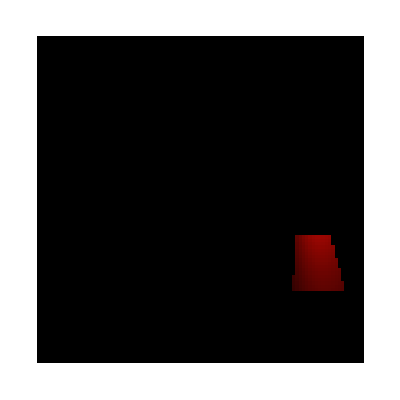

```mathematica
gPrint["Rendered Scene"];
ClearAll[scene,colorMul,imgTable];
scene=pbrtLoadScene["pbrtTestScene.scene"];
colorMul=10;
imgTable=pbrtRenderTile[{77,61},{93,77},scene,colorMul];
Show[ArrayPlot[imgTable]]
```

```mathematica
gPrint["Switch Scenes"];
ClearAll[scene,colorMul,imgTable,renderedFlag];
scene=pbrtLoadScene["pbrtTestScene.scene"];
colorMul=10;
imgTable=Table[1,scene["resx"],scene["resy"]];
renderedFlag=False;
Manipulate[
Show[
If[renderedFlag,
	ArrayPlot[imgTable],
	pbrtPlotOriginScene[scene]],

pbrtPlot3DOptions[scene]
],
Button["Rendered",renderedFlag=!renderedFlag],
Button["Start",imgTable=pbrtRenderTile[{77,61},{93,77},scene,colorMul]],
{{colorMul,10},1,20}
]
```

Switch Scenes

Show::gtype: If is not a type of graphics.

```mathematica
gPrint["Pixel Log"];
ClearAll[scene,l1,log1,l2,log2];
scene=pbrtLoadScene["pbrtTestScene.scene"];
l1=pbrtSamplerIntegratorRender[{51,12},scene,2];
log1=pbrtCurrPixelLog;
l2=pbrtSamplerIntegratorRender[{78,80},scene];
log2=pbrtCurrPixelLog;
pbrtLogPrintPixel[log1];
(*pbrtLogPrintPixel[log2];*)
```

Pixel Log

pixel

{51,12}

cameraRay

<|o→{278.,-800.,273.},d→{0.00986832,0.96904,0.246708}|>

bounce_0

-->base

<|index→0,le→{20.7467,10.8234,2.76459},leBeta→{1,1,1},ld→{0,0,0},ldBeta→{1,1,1},l→{20.7467,10.8234,2.76459}|>

-->misLight

<|l_wo→{-0.00986832,-0.96904,-0.246708},l_wi→{0.400401,0.91634,-1.13658×10^-14},l_lightPdf→5.1592×10^12,l_scatteringPdf→0,l_li→{0,0,0},l_f→{0,0,0},l_lo→{0,0,0}|>

-->misBsdf

<|b_wo→{-0.00986832,-0.96904,-0.246708},b_wi→{0.,0.,-1.},b_lightPdf→0,b_scatteringPdf→0.31831,b_li→{0,0,0},b_f→{6.60389,3.44519,0.879996},b_tr→1,b_lo→{0,0,0}|>

-->nextBounce

<|next_rayo→{289.028,282.915,548.7},next_rayd→{0.,0.,-1.},next_beta→{20.7467,10.8234,2.76459}|>

bounce_1

-->base

<|index→1,le→{0,0,0},leBeta→{20.7467,10.8234,2.76459},ld→{0.133376,0.0546692,0.0133624},ldBeta→{20.7467,10.8234,2.76459},l→{2.76711,0.591706,0.0369416}|>

-->misLight

<|l_wo→{0.,0.,1.},l_wi→{0.0145886,0.0333868,0.999336},l_lightPdf→44.2011,l_scatteringPdf→0.318099,l_li→{20.7467,10.8234,2.76459},l_f→{0.282319,0.221816,0.212259},l_lo→{0.132418,0.0542765,0.0132664}|>

-->misBsdf

<|b_wo→{0.,0.,1.},b_wi→{0.,0.,1.},b_lightPdf→44.1131,b_scatteringPdf→0.31831,b_li→{20.7467,10.8234,2.76459},b_f→{0.282319,0.221816,0.212259},b_tr→1,b_lo→{0.000958038,0.000392689,0.0000959821}|>

-->nextBounce

<|next_rayo→{289.028,282.915,0.},next_rayd→{0.,0.,1.},next_beta→{18.4009,7.54233,1.84352}|>

li

{23.5138,11.4151,2.80153}

```mathematica
gPrint["Validate Pixel"];
ClearAll[scene,testData];
scene=pbrtLoadScene["pbrtTestScene.scene"];
testData=ToExpression[Import["pbrtTestData.pixels"]];
pbrtValidateSinglePixel[51,12,scene,testData]
```

Validate Pixel

{True,{20.7467,10.8234,2.76459},{20.7467,10.8234,2.76459}}

```mathematica
gPrint["Validate Tile"];
ClearAll[scene,testData];
scene=pbrtLoadScene["pbrtTestScene.scene"];
testData=ToExpression[Import["pbrtTestData.pixels"]];
pbrtValidateTilePixels[{45,0},{61,13},scene,testData]
(*pbrtValidateTilePixels[{45,0},{46,1},scene,testData]*)
```

Validate Tile

<|total→208,ok→208,fail→0,black→193|>

```mathematica
gPrint["Plot Path"];
ClearAll[scene,l,pixelLog];
scene=pbrtLoadScene["cornell-tiny.scene"];
l=pbrtSamplerIntegratorRender[{51,12},scene,2];
pixelLog=pbrtCurrPixelLog;
(*pbrtLogPrintPixel[pixelLog];*)
pbrtPlotPath[scene,pixelLog]
```

Plot Path

{<|origin→{278.,-800.,273.},dir→{0.00986832,0.96904,0.246708},length→1117.51|>,<|origin→{289.028,282.915,548.7},dir→{0.,0.,-1.},length→548.7|>,<|origin→{289.028,282.915,0.},dir→{0.,0.,1.},length→100|>}

-Graphics3D-